```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY201/sec_int_data/610nm.dat"]
```

{{1.59376,0.232856},{1.5163,0.250837},{1.45822,0.252935},{1.41492,0.243417},{1.36475,0.247953},{1.33366,0.265206},{1.2821,0.268499},{1.25075,0.267811},{1.2275,0.263364},{1.20277,0.267658},{1.18632,0.275812},{1.16701,0.265973},{1.14926,0.25712},{1.12973,0.219457},{1.10588,-1.1487},{1.11907,0.223064},{1.13878,0.31678},{1.30525,0.266816},{1.35407,0.220259}}

-0.609354+0.618716 x

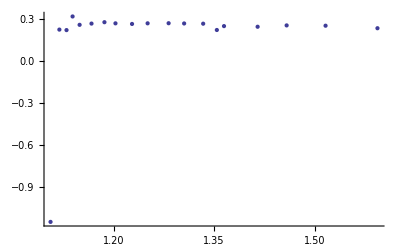

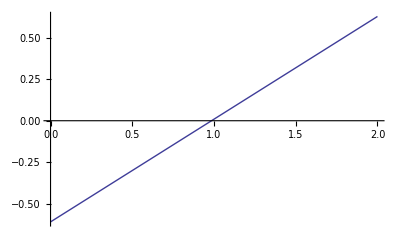

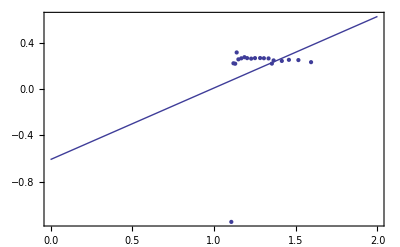

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```